```mathematica
<<Graphics`ImplicitPlot`
```

General::obspkg: "Graphics`ImplicitPlot`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

```mathematica
(* final version in which I find that Michel's solution for sub-Alfvenic flow at the star is the correct minimum-torque solution, is smooth and extends from the star all the way to infinity *)
myu0=0.4;
mysigma=10^3;
myomega=0.25;
mya=mysigma^(1/2)/myomega;
quartic:=A1 x^4+B1 x^2+C1
(*sol=Block[{A1,B1,C1},Solve[quartic==0,{x}]]*)
A1:=(1+u^2)(u+σ)^2-μ^2 u^2
B1:=-2(1+u^2)(u+σ)+2μ u(μ-σ λ)+σ(μ-λ(σ+u))^2
C1:=1+u^2-(μ-σ λ)^2
solmu=Solve[A1==0,{μ}]/.{u->uinf};
mymu=μ/.solmu[[2]] (* pick the positive number *)
quarticstar:=quartic//.{μ->mymu,x->1/a,a->σ^(1/2)/Ω,u->u0}
quarticstarmu:=quartic//.{x->1/a,a->σ^(1/2)/Ω}
quarticstarnummu:=quarticstarmu//.{u->myu0,σ->mysigma,Ω->myomega}
quarticstarnum=quarticstar//.{u0->myu0,σ->mysigma,Ω->myomega};
quarticallx:=quartic//.{a->σ^(1/2)/Ω}
quarticstarnumallx:=quarticallx//.{σ->mysigma,Ω->myomega,μ->mymu};
(*FullSimplify[quarticstar]*)
(*Solve[0==quarticstar,{uinf}]*)

uinfminsol = Solve[D[(√(1+uinf^2) (uinf+σ))/uinf,uinf]==0,{uinf}]
(* Constraints from infinity: at infinity μ ≥ mymumin &*)
uinfmin = uinfminsol[[1,1,2]]
uinfminnum=uinfmin//.σ->mysigma
mymumin1anal=FullSimplify[(√(1+uinf^2) (uinf+σ))/uinf/.uinf->uinfmin];
mymumin1=mymumin1anal//.σ->mysigma
(* Constraints from the star: at the star A1 B1 < 0 so that the larger root in x extends to infinity as u -> uinf *)
mymumin2=Solve[0==A1//.{u->myu0,σ->mysigma},{μ}][[2,1,2]]
mymumin=1.Min[mymumin1,mymumin2]
mylambdasol=Solve[0==quarticstarnummu//.{μ->mymumin,σ->mysigma},{λ}]
mylambdamin =mylambdasol[[1,1,2]]

(μ-λ σ)/λ//.{σ->mysigma,λ->mylambdamin,μ->mymumin}
```

(√(1+uinf^2) (uinf+σ))/uinf

{{uinf→σ^(1/3)},{uinf→-(-1)^(1/3) σ^(1/3)},{uinf→(-1)^(2/3) σ^(1/3)}}

σ^(1/3)

10

101 √101

2693.66

1015.04

{{λ→1.01399},{λ→1.01609}}

1.01399

1.03329

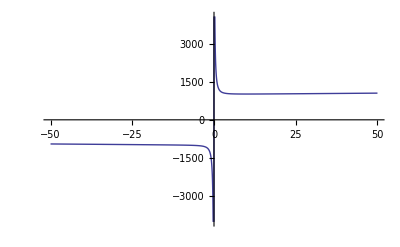

```mathematica
(* Plot relation between μ and the asymptotic radial 4-velocity *)
Plot[(√(1+uinf^2) (uinf+σ))/uinf/.σ->mysigma,{uinf,-50,50}]
```

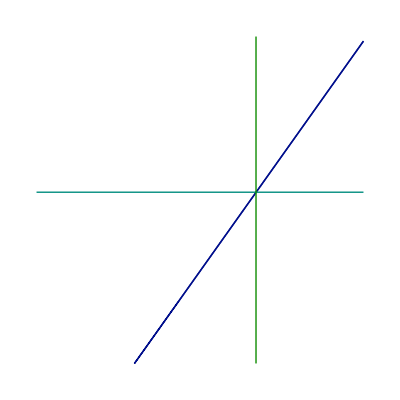

```mathematica
(* Shows the following curves in (λ, μ) plane:
1. quarticstarnum==0
two parallel curves going at an angle to the axes -- relation between μ and λ due to star boundary condition;
  2. λ == lambdamin
  shows the minimal torque value;
  3. 0 == A1/.{at the star surface}
  shows where the quartic becomes degenerate; I am not sure, but it seems that one has to have μ lying below this line in order for a solution to get to infinity;
*)
Clear[λ,μ]
res=ImplicitPlot[{quarticstarnummu==0,μ==mymumin1/.σ->mysigma,λ==mylambdamin,0==A1//.{u->myu0,σ->mysigma}},{λ,-1,2 },{μ,-0.1mymumin/.σ->mysigma,2*mymumin/.σ->mysigma},PlotPoints->500,AspectRatio->1]
```

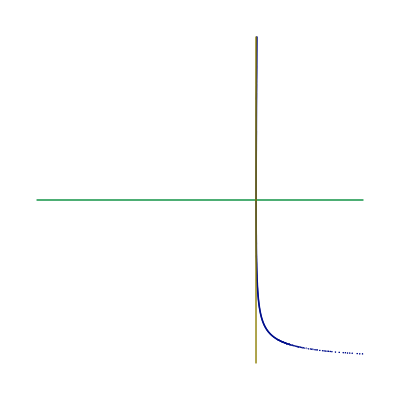

```mathematica
(* Similar to the above plot but in (λ,uinfinity) plane *)
res=ImplicitPlot[{quarticstarnum==0,uinf==mysigma^{1/3},λ==mylambdamin},{λ,-1,2},{uinf,myu0/10^10,2 mysigma^(1/3)},PlotPoints->500,AspectRatio->1]
```

```mathematica
Clear[uinf,myuinf,λ];
mylambda=mylambdamin;(* mylambdamin;*)(*lambdaminrealnum;*)
myquart=quarticstarnum//.{λ->mylambda};

(* for a given λ, find such uinf that at the star u = u0 *)

mymusol=Solve[0==quarticstarnummu//.{λ->mylambda,σ->mysigma},{μ}]
mymu= mymusol[[Length[mymusol],1,2]];

myuinfsol=Solve[(√(1+uinf^2) (uinf+σ))/uinf==mymu,{uinf}]//.{σ->mysigma}
myuinf=Re[myuinfsol[[Length[myuinfsol]-1,1,2]]];

Print["u0=",myu0,"     ucr= ",(μ-λ σ)/λ//.{μ->mymu,λ->mylambda,σ->mysigma,uinf->myuinf},"    uinf=",myuinf,"  lambda=",mylambda, "  mu=", mymu];

myquart=quarticstarnumallx//.{λ->mylambda};
mysolve=Solve[myquart==0,x];
soll=mysolve;

fun1=mya*x/.(soll[[1]]);
fun2=mya*x/.(soll[[2]]);
fun3=mya*x/.(soll[[3]]);
fun4=mya*x/.(soll[[4]]);
nfun1=If[Abs[Im[fun1]]<10^(-5),Re[fun1],10^(-10)*I];
nfun2=If[Abs[Im[fun2]]<10^(-5),Re[fun2],10^(-10)*I];
nfun3=If[Abs[Im[fun3]]<10^(-5),Re[fun3],10^(-10)*I];
nfun4=If[Abs[Im[fun4]]<10^(-5),Re[fun4],10^(-10)*I];
nnfun1=Log[10,Abs[nfun1]]+UnitStep[-nfun1] I;
nnfun2=Log[10,Abs[nfun2]]+UnitStep[-nfun2] I;
nnfun3=Log[10,Abs[nfun3]]+UnitStep[-nfun3] I;
nnfun4=Log[10,Abs[nfun4]]+UnitStep[-nfun4] I;


mypl=Plot[{nnfun1,nnfun2,nnfun3,Evaluate[nnfun4]},{u,-10Min[myu0,myuinf],10Max[myu0,myuinf]},PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,0,1],RGBColor[0.,0.7,0.7]},PlotPoints->10000,AxesLabel->{u,"Log(ax)"},PlotRange->{All,{-0.5,4}}];
```

{{μ→1012.94},{μ→1015.04}}

{{uinf→-2015.04},{uinf→-4.96269},{uinf→10.-0.0000285466 ⅈ},{uinf→10.+0.0000285466 ⅈ}}

u0=0.4     ucr= 1.03329    uinf=10.  lambda=1.01399  mu=1015.04

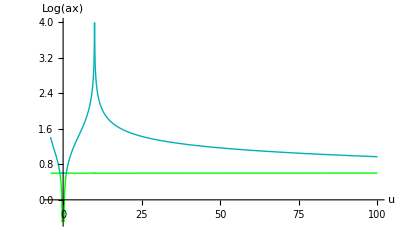

```mathematica
Show[mypl]
```

```mathematica
(* rows=which uinf, columns=which root for x(u) *)
matrixcol={fun1,fun2,fun3,fun4};
matrixx=Table[matrixcol[[j]],{i,1,Length[myuinfsol]},{j,1,4}];
matrixxatuinf=Table[matrixx[[i,j]]//.{u->0.999999uinf}//.myuinfsol[[i]],{i,1,Length[myuinfsol]},{j,1,4}]
MatrixForm[matrixxatuinf]
```

```mathematica
(* To manually check the signs of coefficients and values of roots *)
myassigns={μ->mymu,σ->mysigma,u->Re[myuinf],λ->mylambda}
Print["sols"];
((-B1-(B1^2-4A1 C1)^(1/2))/(2 A1))^(1/2)//.myassigns
((-B1+(B1^2-4A1 C1)^(1/2))/(2 A1))^(1/2)//.myassigns
Print["Parts"];
(-B1-(B1^2-4A1 C1)^(1/2))//.myassigns

(-B1+(B1^2-4A1 C1)^(1/2))//.myassigns
Print["other"]

A1//.myassigns
B1//.myassigns
C1//.myassigns

A1//.{μ->mymu,σ->mysigma,u->myu0,λ->mylambda}
mya((-B1-(B1^2-4A1 C1)^(1/2))/(2 A1))^(1/2)//.{μ->mymu,σ->mysigma,u->myu0,λ->mylambda}

Print["coeffs"]
A1//.{λ->mylambdamin,μ->mymumin,u->myu0,σ->mysigma}
B1//.{λ->mylambdamin,μ->mymumin,u->myu0,σ->mysigma}
C1//.{λ->mylambdamin,μ->mymumin,u->myu0,σ->mysigma}
```

{μ→1015.04,σ→1000,u→10.,λ→1.01399}

sols

0.0315877

61969.

Parts

5.20085×10^-8

200166.

other

0.0000260621

-100083.

99.9022

996080.

1.

coeffs

996080.

-1057.76

0.0622191